# Explicit closed form derivatives of Black Scholes formula with respect to volatility

## Black Scholes Option Pricing Formula

```mathematica
x
```

x

```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
normalCDF[d_]:=1/2(1+Erf[d/(√2)]);
logForward[S_,K_,T_,r_]:= Log[S/K]+r*T;
Std[σ_,T_]:= σ √T;
d1[lo_,Z_]:=lo/Z+Z/2;
d2[lo_,Z_]:=lo/Z-Z/2;
BSCall[S_,lo_,Z_]:=S (normalCDF[d1[lo,Z]]-Exp[-lo]normalCDF[d2[lo,Z]]);
BSCallHandy[S_,K_,T_,r_,σ_]:=S normalCDF[d1[logForward[S,K,T,r],Std[σ,T]]]-K Exp[-r T]normalCDF[d2[logForward[S,K,T,r],Std[σ,T]]];

BSPut[S_,lo_,Z_]:=S(-normalCDF[-d1[lo,Z]]+Exp[-lo]normalCDF[-d2[lo,Z]]);
BSPutHandy[S_,K_,T_,r_,σ_]:=-S normalCDF[-d1[logForward[S,K,T,r],Std[σ,T]]]+K Exp[-r T]normalCDF[-d2[logForward[S,K,T,r],Std[σ,T]]];
```

## Priori-checking

```mathematica
D[BSCallHandy[Exp[x],K,T,r,σ],{x,1}]//Simplify
```

1/2 ⅇ^x (1+Erf[(T (2 r+σ^2)+2 Log[ⅇ^x/K])/(2 √2 √T σ)])

```mathematica
dxCall[S_,K_,T_,r_,σ_,q_,l_]:=
S Exp[-q T] normalCDF[d1[logForward[S,K,T,r],Std[σ,T]]]+K Exp[-r T] Exp[-0.5*d2[logForward[S,K,T,r],Std[σ,T]]^2]/(√(2 Pi) σ √T) ∑_(i=0)^(l-2) HermiteH[i,d2[logForward[S,K,T,r],Std[σ,T]]/(√2)]/(- σ √T)^i 2^((- i)/2);
d1x[x_,K_,T_,r_,σ_]:=(x+r T - Log[K]+ (σ^2 T)/2)/(σ √T);

dxCall2[x_,K_,T_,r_,σ_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=d1/(√2);
Exp[x]/2(1+Erf[g]) + Exp[x] 1/2∑_(j=1)^n Binomial[n,j](√2 σ √T)^-j ((-1)^(j-1) 2/(√Pi) HermiteH[j-1,g] Exp[- g^2])
];
dxCall3[x_,K_,T_,r_,σ_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=d1/(√2);
Exp[x]/2 (1+∑_(j=0)^n Binomial[n,j] ND[Erf[d1x[xx,K,T,r,σ]/(√2)],{xx,j},x])];
dxCall4[x_,K_,T_,r_,σ_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=d1/(√2);
Exp[x]/2 (1+∑_(j=0)^n Binomial[n,j] 2/(√Pi) Exp[-g^2] HermiteH[j,g] (σ √(2 T))^-j )];
```

### Check n-the derivative of Erf function: Hermite polynomial

```mathematica
x
```

x

```mathematica
Table[{{HermiteH[n,x],2^(-n/2) HermiteH[n,x/√2]},{D[Erf[x],{x,n+1}],2/(√Pi) Exp[-x^2] HermiteH[n,x]}},{n,0,6,1}]//Simplify
```

{{{1,1},{(2 ⅇ^(-x^2))/(√π),(2 ⅇ^(-x^2))/(√π)}},{{2 x,x},{-(4 ⅇ^(-x^2) x)/(√π),(4 ⅇ^(-x^2) x)/(√π)}},{{-2+4 x^2,-1+x^2},{(ⅇ^(-x^2) (-4+8 x^2))/(√π),(ⅇ^(-x^2) (-4+8 x^2))/(√π)}},{{4 x (-3+2 x^2),x (-3+x^2)},{-(8 ⅇ^(-x^2) x (-3+2 x^2))/(√π),(8 ⅇ^(-x^2) x (-3+2 x^2))/(√π)}},{{4 (3-12 x^2+4 x^4),3-6 x^2+x^4},{(8 ⅇ^(-x^2) (3-12 x^2+4 x^4))/(√π),(8 ⅇ^(-x^2) (3-12 x^2+4 x^4))/(√π)}},{{8 x (15-20 x^2+4 x^4),x (15-10 x^2+x^4)},{-(16 ⅇ^(-x^2) x (15-20 x^2+4 x^4))/(√π),(16 ⅇ^(-x^2) x (15-20 x^2+4 x^4))/(√π)}},{{8 (-15+90 x^2-60 x^4+8 x^6),-15+45 x^2-15 x^4+x^6},{(16 ⅇ^(-x^2) (-15+90 x^2-60 x^4+8 x^6))/(√π),(16 ⅇ^(-x^2) (-15+90 x^2-60 x^4+8 x^6))/(√π)}}}

### Check n-th derivatives of composite function

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,q=0,x,g},
x=Log[S];
g=d1x[x,K,T,r,σ]/(√2);
Table[{
{n,ND[Erf[d1x[xx,K,T,r,σ]/(√2)],{xx,n},x]},
{2/(√Pi) Exp[-g^2] HermiteH[n-1,g](-1)^(n-1)(σ √(2T))^-n,ND[Erf[xx],{xx,n},g](σ √(2T))^-n},
{D[Erf[y],{y,n}],(-1)^(n-1)2/(√Pi) Exp[-y^2] HermiteH[n-1,y] },
{D[Erf[y],{y,n}],(-1)^(n-1)2/(√Pi) Exp[-y^2] HermiteH[n-1,y] }/.y->g,
{(-1)^(n-1)2/(√Pi) Exp[-g^2] HermiteH[n-1,g],
ND[Erf[xx],{xx,n},g]}
},{n,1,10,1}]
]//Simplify
```

{{{1,2.52955},{2.52955,2.52955},{(2 ⅇ^(-y^2))/(√π),(2 ⅇ^(-y^2))/(√π)},{1.0732,1.0732},{1.0732,1.0732}},{{2,-2.67067},{-2.67008,-2.67009},{-(4 ⅇ^(-y^2) y)/(√π),-(4 ⅇ^(-y^2) y)/(√π)},{-0.480615,-0.480615},{-0.480615,-0.480616}},{{3,-25.2503},{-25.2877,-25.2878},{(ⅇ^(-y^2) (-4+8 y^2))/(√π),(ⅇ^(-y^2) (-4+8 y^2))/(√π)},{-1.93116,-1.93116},{-1.93116,-1.93116}},{{4,85.4391},{86.0278,86.0419},{-(8 ⅇ^(-y^2) y (-3+2 y^2))/(√π),-(8 ⅇ^(-y^2) y (-3+2 y^2))/(√π)},{2.7873,2.7873},{2.7873,2.78776}},{{5,741.58},{752.117,751.749},{(8 ⅇ^(-y^2) (3-12 y^2+4 y^4))/(√π),(8 ⅇ^(-y^2) (3-12 y^2+4 y^4))/(√π)},{10.3387,10.3387},{10.3387,10.3337}},{{6,-4130.51},{-4617.36,-4619.94},{-(16 ⅇ^(-y^2) y (15-20 y^2+4 y^4))/(√π),-(16 ⅇ^(-y^2) y (15-20 y^2+4 y^4))/(√π)},{-26.9284,-26.9284},{-26.9284,-26.9435}},{{7,-41826.4},{-36910.4,-36651.},{(16 ⅇ^(-y^2) (-15+90 y^2-60 y^4+8 y^6))/(√π),(16 ⅇ^(-y^2) (-15+90 y^2-60 y^4+8 y^6))/(√π)},{-91.3277,-91.3277},{-91.3277,-90.6858}},{{8,282523.},{346785.,343203.},{-(32 ⅇ^(-y^2) y (-105+210 y^2-84 y^4+8 y^6))/(√π),-(32 ⅇ^(-y^2) y (-105+210 y^2-84 y^4+8 y^6))/(√π)},{364.041,364.041},{364.041,360.281}},{{9,4.62747×10^6},{2.50476×10^6,2.37508×10^6},{(32 ⅇ^(-y^2) (105-840 y^2+840 y^4-224 y^6+16 y^8))/(√π),(32 ⅇ^(-y^2) (105-840 y^2+840 y^4-224 y^6+16 y^8))/(√π)},{1115.56,1115.56},{1115.56,1057.8}},{{10,-4.45878×10^7},{-3.34692×10^7,7.88709×10^7},{-(64 ⅇ^(-y^2) y (945-2520 y^2+1512 y^4-288 y^6+16 y^8))/(√π),-(64 ⅇ^(-y^2) y (945-2520 y^2+1512 y^4-288 y^6+16 y^8))/(√π)},{-6324.24,-6324.24},{-6324.24,14903.2}}}

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,q=0},
Table[{{l,
ND[BSCallHandy[Exp[x],K,T,r,σ],{x,l},Log[100]]}, 
dxCall[S,K,T,r,σ,q,l],
dxCall2[Log[S],K,T,r,σ,l-1],
dxCall3[Log[S],K,T,r,σ,l-1],
dxCall4[Log[S],K,T,r,σ,l-1]
},{l,0,10,1}]
]
With[{S=100,K=100,T=1,r=0.05,σ=0.3,l=2},
{BSCallHandy[S,K,T,r,σ],ND[BSCallHandy[Exp[x],K,T,r,σ],{x,l},Log[100]],dxCall2[Log[S],K,T,r,σ,l-1],dxCall[S,K,T,r,σ,l]}]
```

{{{0,14.2313},62.4252,62.4252,50,50},{{1,62.4252},62.4252,62.4252,62.4252,103.66},{{2,188.905},188.903,188.903,188.903,160.301},{{3,181.66},181.876,181.876,181.847,-319.492},{{4,-1217.43},-1223.04,-1223.04,-1221.26,-3160.64},{{5,-989.894},-988.844,-988.844,-1010.97,5766.73},{{6,43514.},45828.7,45828.7,45173.1,154496.},{{7,70478.9},32819.,32819.,53595.6,-73.3223},{{8,-2.47858×10^6},-2.56743×10^6,-2.56743×10^6,-2.65487×10^6,-1.02966×10^7},{{9,-1.16966×10^7},-1.55566×10^6,-1.55566×10^6,-6.08505×10^6,-2.11557×10^7},{{10,3.04503×10^8},2.0063×10^8,2.0063×10^8,2.70974×10^8,8.71773×10^8}}

{14.2313,188.905,188.903,dxCall[100,100,1,0.05,0.3,2]}

## n-th derivative of option pricing formula

### With respect to x

```mathematica
DxV[x_,K_,T_,r_,σ_,c_,n_]:=Module[{d1=d1x[x,K,T,r,σ],g},
g=c*d1/(√2);
c*Exp[x]/2(1+Erf[g]) + c*Exp[x] 1/2∑_(j=1)^(n-1) Binomial[n-1,j](c*√2 σ √T)^-j ((-1)^(j-1) 2/(√Pi) HermiteH[j-1,g] Exp[- g^2])
];
NDxV[x_,K_,T_,r_,σ_,c_,n_]:=If[c==1, ND[BSCallHandy[Exp[xx],K,T,r,σ],{xx,n},x],
 ND[BSPutHandy[Exp[xx],K,T,r,σ],{xx,n},x]];
```

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3},
Table[{DxV[x,K,T,r,σ,c,n],NDxV[x,K,T,r,σ,c,n]}, {n,1,4,1},{c,-1,1,2}]]//MatrixForm
```

((-37.5748
-37.5748) | (62.4252
62.4252)
(88.9028
88.9047) | (188.903
188.905)
(81.8763
81.6601) | (181.876
181.66)
(-1323.04
-1317.43) | (-1223.04
-1217.43))

### With respect to volatility

```mathematica
Table[BellY[n,n-1,{x,y}],{n,2,10,1}]
```

{y,3 x y,6 x^2 y,10 x^3 y,15 x^4 y,21 x^5 y,28 x^6 y,36 x^7 y,45 x^8 y}

```mathematica
DvV[x_,K_,T_,r_,σ_,c_,n_]:=∑_(k=1)^n (n!)/((2k-n)! (n-k)!) (T^k σ^(2k-n))/2^(n-k)∑_(j=0)^k Binomial[k,j] (-1)^(k-j)DxV[x,K,T,r,σ,c,k+j];

NDvV[x_,K_,T_,r_,σ_,c_,n_]:=If[c==1, ND[BSCallHandy[Exp[x],K,T,r,xx],{xx,n},σ],
 ND[BSPutHandy[Exp[x],K,T,r,xx],{xx,n},σ]];
```

### Comparison with numerical method, we can see the numerical one bear some error in high order cases

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3},
Table[{DvV[x,K,T,r,σ,c,n],NDvV[x,K,T,r,σ,c,n]}, {n,1,5,1},{c,-1,1,2}]]//MatrixForm
```

((37.9433
37.9433) | (37.9433
37.9433)
(0.667521
0.661521) | (0.667521
0.661521)
(-44.6068
-44.1638) | (-44.6068
-44.1638)
(466.081
444.237) | (466.081
444.237)
(-7616.98
-6721.4) | (-7616.98
-6721.4))

### Taylor series coefficients comparison

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3},
Table[{DvV[x,K,T,r,σ,c,n]/(n!),NDvV[x,K,T,r,σ,c,n]/(n!)}, {n,1,10,1},{c,-1,1,2}]]//MatrixForm
```

((37.9433
37.9433) | (37.9433
37.9433)
(0.33376
0.33076) | (0.33376
0.33076)
(-7.43446
-7.36064) | (-7.43446
-7.36064)
(19.42
18.5099) | (19.42
18.5099)
(-63.4748
-56.0117) | (-63.4748
-56.0117)
(208.285
161.518) | (208.285
161.518)
(-681.132
-438.26) | (-681.132
-438.261)
(2221.53
1120.2) | (2221.53
1120.23)
(-7225.8
-2705.) | (-7225.8
-2705.43)
(23436.1
6192.47) | (23436.1
6198.21))

### Exactly what we got from Taylor series

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05},Series[BSCallHandy[Exp[x],K,T,r,σ],{σ,0.3,10}]]
```

14.2313+37.9433 (σ-0.3)+0.33376 (σ-0.3)^2-7.43446 (σ-0.3)^3+19.42 (σ-0.3)^4-63.4748 (σ-0.3)^5+208.285 (σ-0.3)^6-681.132 (σ-0.3)^7+2221.53 (σ-0.3)^8-7225.8 (σ-0.3)^9+23436.1 (σ-0.3)^10+O[σ-0.3]^11

## Visualize the function

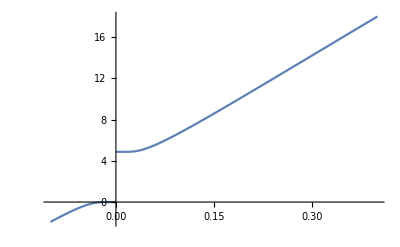

```mathematica
With[{S=100,K=100,T=1,r=0.05},
Plot[BSCallHandy[S,K,T,r,x],{x,-0.1,0.4}]]
```

```mathematica
f[z_]:=With[{S=100,K=100,T=1,r=0.05},
BSCallHandy[S,K,T,r,σ]]/.σ->z;
f2[z_]:=With[{x=Log[100],K=100,T=1,r=0.05},Normal[Series[BSCallHandy[Exp[x],K,T,r,σ],{σ,0.3,10}]]]/.σ->z
u[{x_,y_}]:=Re[f[x+I y]];
v[{x_,y_}]:=Im[f[x+I y]];
Φ[{x_,y_}]:={u[{x,y}],v[{x,y}]};
Φ̄[{x_,y_}]:={u[{x,y}],-v[{x,y}]};
SuperStar[Φ][{x_,y_}]:={v[{x,y}],u[{x,y}]};
u2[{x_,y_}]:=Re[f2[x+I y]];
v2[{x_,y_}]:=Im[f2[x+I y]];
```

```mathematica
Plot3D[{u[{x,y}],v[{x,y}]},{x,-0.0,0.1},{y,-0.1,0.1},MeshFunctions->{#3&},Mesh->15]
Plot3D[{u2[{x,y}],v2[{x,y}]},{x,-0.0,0.1},{y,-0.1,0.1},MeshFunctions->{#3&},Mesh->15]
```

-Graphics3D-

-Graphics3D-

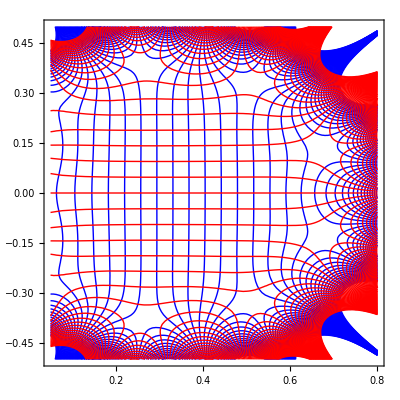

```mathematica
Show[ContourPlot[u2[{x, y}], {x, 0.05, 0.8}, {y, -0.5, 0.5},Contours->50,ContourStyle->{Blue},ContourShading -> None] ,
 ContourPlot[v2[{x, y}], {x, 0.05, 0.8}, {y, -0.5, 0.5},Contours->50,ContourStyle->{Red} ,ContourShading -> None]]
```

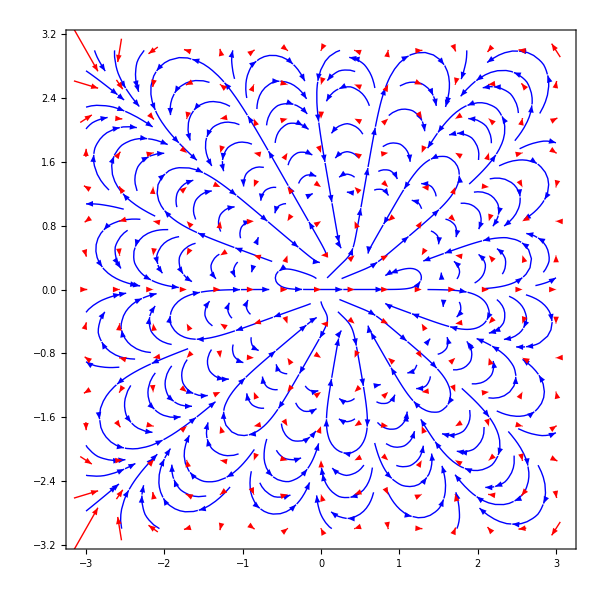

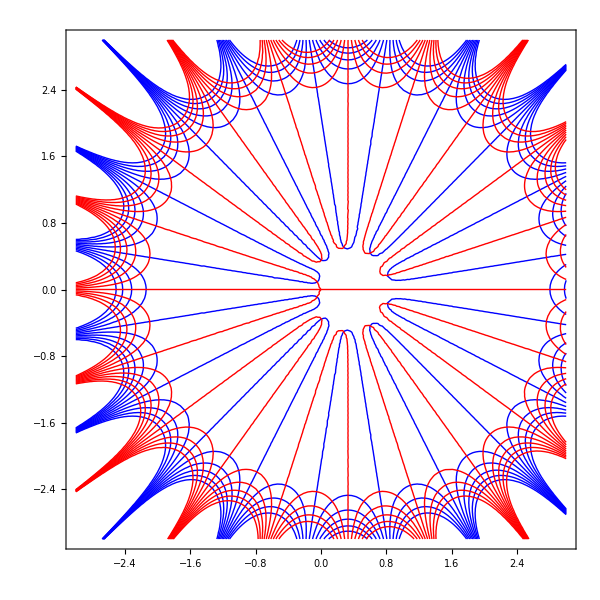

Show::gcomb: Could not combine the graphics objects in Show[StreamPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},StreamStyle→Blue],VectorPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},VectorStyle→Red],ImageSize→600].

```mathematica
Show[StreamPlot[{u2[{x,y}],v2[{x,y}]},{x,-3,3},{y,-3,3},StreamStyle->Blue],
	VectorPlot[{u2[{x,y}],v2[{x,y}]},{x,-3,3},{y,-3,3},VectorStyle->Red],ImageSize->600]
Show[ContourPlot[u2[{x, y}], {x, -3, 3}, {y, -3, 3},Contours->10,ContourStyle->{Blue},ContourShading -> None] ,
 ContourPlot[v2[{x, y}], {x, -3, 3}, {y, -3, 3},Contours->10,ContourStyle->{Red} ,ContourShading -> None]]
```

## Explicit inversion series

```mathematica
x
```

x

```mathematica
With[{n=7},SeriesData[x,0,Array[a,n],1,n+1,1]]
With[{n=7},CoefficientList[InverseSeries[SeriesData[x,0,Array[a,n],1,n+1,1]],x]]
```

a[1] x+a[2] x^2+a[3] x^3+a[4] x^4+a[5] x^5+a[6] x^6+a[7] x^7+O[x]^8

{0,1/a[1],-a[2]/a[1]^3,(2 a[2]^2-a[1] a[3])/a[1]^5,(-5 a[2]^3+5 a[1] a[2] a[3]-a[1]^2 a[4])/a[1]^7,(14 a[2]^4-21 a[1] a[2]^2 a[3]+3 a[1]^2 a[3]^2+6 a[1]^2 a[2] a[4]-a[1]^3 a[5])/a[1]^9,1/a[1]^11(-42 a[2]^5+84 a[1] a[2]^3 a[3]-28 a[1]^2 a[2] a[3]^2-28 a[1]^2 a[2]^2 a[4]+7 a[1]^3 a[3] a[4]+7 a[1]^3 a[2] a[5]-a[1]^4 a[6]),1/a[1]^13(132 a[2]^6-330 a[1] a[2]^4 a[3]+180 a[1]^2 a[2]^2 a[3]^2-12 a[1]^3 a[3]^3+120 a[1]^2 a[2]^3 a[4]-72 a[1]^3 a[2] a[3] a[4]+4 a[1]^4 a[4]^2-36 a[1]^3 a[2]^2 a[5]+8 a[1]^4 a[3] a[5]+8 a[1]^4 a[2] a[6]-a[1]^5 a[7])}

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,fixVol=0.3,c=1},
fArray:=k↦Table[DvV[x,K,T,r,fixVol,c,j],{j,1,k}];
fArray:=k↦Table[DvV[x,K,T,r,fixVol,c,j+1]/((j+1) DvV[x,K,T,r,fixVol,c,1]),{j,1,k}];
fArray@5
]
```

{0.0087963,-0.391872,3.07091,-40.1493,658.726}

```mathematica
x
```

x

```mathematica
DpV[S_,K_,T_,r_,c_,Price_,fixVol_,n_]:=Module[{x,z,f,fHat,fHatArray,g},
x=Log[S];
z=If[c==1,Price - BSCallHandy[S,K,T,r,fixVol],Price-BSPutHandy[S,K,T,r,fixVol]];
f:=k↦DvV[x,K,T,r,fixVol,c,k];
fHat:=k↦f[k+1]/((k+1) f[1]);
fHatArray:=k↦Table[fHat[j],{j,1,k}];
g = Which[
n==0,0,
n==1,1/f[1],
n≥2, 1/f[1]^n∑_(k=1)^(n-1) (-1)^k ((n+k-1)!)/((n-1)!) BellY[n-1,k,fHatArray[n-k]]];
g
];
Module[{x=Log[100],S=100,K=100,T=1,r=0.05,σ=0.3,fixVol=0.2,c=1,n=7,truePrice,fixPrice,dpVArray,vol,gk},
truePrice = If[c==1,BSCallHandy[S,K,T,r,σ],BSPutHandy[S,K,T,r,σ]];
fixPrice = If[c==1,BSCallHandy[S,K,T,r,fixVol],BSPutHandy[S,K,T,r,fixVol]];
dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];
gk=k↦DpV[S,K,T,r,c,truePrice,fixVol,k];
vol =fixVol+ ∑_(k=1)^n gk[k]/(k!) (truePrice-fixPrice)^k]
```

0.300028

```mathematica
VolOfPrice[S_,K_,T_,r_,price_,c_,fixVol_,n_]:=Module[{x=Log[S],truePrice=price,fixPrice,dpVArray,vol,gk},
fixPrice = If[c==1,BSCallHandy[S,K,T,r,fixVol],BSPutHandy[S,K,T,r,fixVol]];
dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];
gk=k↦DpV[S,K,T,r,c,truePrice,fixVol,k];
vol =fixVol+ ∑_(k=1)^n gk[k]/(k!) (truePrice-fixPrice)^k];
```

```mathematica
x
```

x

```mathematica
Module[{S=100,K=80,T=1,r=0.05,trueVol=0.3,truePrice,volEstimation},
truePrice = BSCallHandy[S,K,T,r,trueVol];
Table[volEstimation=VolOfPrice[S,K,T,r,truePrice,1,fixVol,n],{fixVol,0.05,1,0.1},{n,5,10,3}]//MatrixForm
]
```

(1.66033×10^37 | -3.06428×10^61
934.655 | -1.2702×10^6
0.300238 | 0.299955
0.300006 | 0.3
0.300507 | 0.300068
0.302221 | 0.300537
0.304854 | 0.301564
0.307951 | 0.303045
0.311188 | 0.304822
0.314327 | 0.30677)

```mathematica
Manipulate[
Module[{targetCallPrice,estimatedCallPrice,estimatedIV,newtonRoot},

targetCallPrice=BSCallHandy[S,K,T,r,σ];
estimatedIV=VolOfPrice[S,K,T,r,targetCallPrice,1,a,order];
newtonRoot = Timing[FindRoot[BSCallHandy[S,K,T,r,xx]==targetCallPrice,{xx,a}]];

{{targetCallPrice},{σ,estimatedIV,newtonRoot}}],
"underlying, S_0",
{{S,100.,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{order,5,""},0,20,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed volatility, a",
{{a,0.3,""},0.05,1,0.1,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3,fixVol=0.3,c=1,price,dxV},
price = BSCallHandy[S,K,T,r,σ];
dxV :=n↦DxV[Log[S],K,T,r,σ,c,n];

Table[Abs[dxV[n]/n!]^(1/n),{n,1,70,5}]
]
```

{62.4252,1.99818,1.08654,1.19378,0.81213,0.960465,0.796877,0.831225,0.731277,0.744952,0.675824,0.68173,0.630361,0.632684}

{0.0263551,0.0358216,0.0556036,0.0662666}

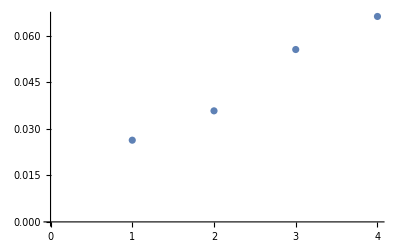

```mathematica
dpVArray = Module[{S=100,K=100,T=1,r=0.05,σ=0.3,fixVol=0.3,c=1,price,dpV},
price = BSCallHandy[S,K,T,r,σ];
dpV =n↦DpV[S,K,T,r,c,price,fixVol,n];
Table[Abs[dpV[n]/n!]^(1/n),{n,1,20,5}]
]
ListPlot[dpVArray]
```

## Invert the log stock price

```mathematica
x
```

x

```mathematica
With[{K=100,T=1,r=0.05,σ=0.3},
Table[DxV[Log[K*Exp[-r T]],K,T,r,σ,1,n],{n,1,10}]]
```

{53.2325,178.313,240.853,-1117.66,-3186.69,41062.4,155144.,-2.2461×10^6,-1.10522×10^7,1.71308×10^8}

```mathematica
Module[{K=100,T=1,r=0.05,σ=0.3},
Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[K],10}]]
```

14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11

```mathematica
InverseSeries[%]
```

Log[100]+0.0160192 (xx-14.2313)-0.000388266 (xx-14.2313)^2+0.0000168251 (xx-14.2313)^3-8.44791×10^-7 (xx-14.2313)^4+4.58395×10^-8 (xx-14.2313)^5-2.61262×10^-9 (xx-14.2313)^6+1.53975×10^-10 (xx-14.2313)^7-9.2973×10^-12 (xx-14.2313)^8+5.71812×10^-13 (xx-14.2313)^9-3.56793×10^-14 (xx-14.2313)^10+O[xx-14.2313]^11

### with respect to S

```mathematica
Manipulate[
Module[{targetCallPrice,SeriesX,estimatedX,newtonRoot},

SeriesX = Series[BSCallHandy[xx,K,T,r,σ],{xx,a,order}];
seriesTable = Table[
{S,
Normal[SeriesX]/.xx->S ,
BSCallHandy[S,K,T,r,σ]},
{S,1,3 K,10}];
estimatedX=Normal[InverseSeries[SeriesX]]/.xx->K2;
estimatedPrice = BSCallHandy[estimatedX,K,T,r,σ];
newtonRoot = Timing[FindRoot[BSCallHandy[xx,K,T,r,σ]==K2,{xx,K}]];

{{K2,(*estimatedPrice,*)estimatedX,newtonRoot},seriesTable}
],
"underlying, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{order,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed volatility, a",
{{a,100,""},0,300,1,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

### with respect to x

```mathematica
x
```

x

```mathematica
With[{x=Log[100],K=100,T=1,r=0.05,σ=0.3,c=1,n=10},
Table[DxV[x,K,T,r,σ,c,k]/k!,{k,1,n}]]
```

{62.4252,94.4514,30.3127,-50.96,-8.24037,63.651,6.51171,-63.6764,-4.28699,55.2882}

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3},
Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[100],10}]]
```

14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11

```mathematica
InverseSeries[%]
```

Log[100]+0.0160192 (xx-14.2313)-0.000388266 (xx-14.2313)^2+0.0000168251 (xx-14.2313)^3-8.44791×10^-7 (xx-14.2313)^4+4.58395×10^-8 (xx-14.2313)^5-2.61262×10^-9 (xx-14.2313)^6+1.53975×10^-10 (xx-14.2313)^7-9.2973×10^-12 (xx-14.2313)^8+5.71812×10^-13 (xx-14.2313)^9-3.56793×10^-14 (xx-14.2313)^10+O[xx-14.2313]^11

```mathematica
%/.xx->BSCallHandy[100,100,1,0.05,0.3]
```

Log[100]

```mathematica
x
```

x

```mathematica
Manipulate[
Module[{targetCallPrice,SeriesX,estimatedX,newtonRoot,estimatedPrice},

SeriesX = Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[a],order}];
seriesTable = Table[
{S,
Normal[SeriesX]/.xx->Log[S],
BSCallHandy[S,K,T,r,σ]},
{S,1/2 K,3 K,10}];
estimatedX=Normal[InverseSeries[SeriesX]]/.xx->K2;
estimatedPrice = BSCallHandy[Exp[estimatedX],K,T,r,σ];
newtonRoot = Timing[FindRoot[BSCallHandy[Exp[xx],K,T,r,σ]==K2,{xx,Log[a]}]];

{{K2,estimatedPrice,Exp[estimatedX],estimatedX,newtonRoot},seriesTable}
],
"underlying, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{order,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed volatility, a",
{{a,100,""},1,400,5,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```

```mathematica
D[BSCallHandy[Exp[x],K,T,r,σ],{xx,2}]/.xx->0
D[BSCall[S,lo,Z],{lo,1}]//Simplify
```

0

1/2 ⅇ^-lo S (1+Erf[(lo/Z-Z/2)/(√2)])

```mathematica
D[BSCallHandy[Exp[xx],K,T,r,σ],{xx,1}]//Simplify
```

1/2 ⅇ^xx (1+Erf[(T (2 r+σ^2)+2 Log[ⅇ^xx/K])/(2 √2 √T σ)])

```mathematica
DpX[K_,T_,r_,σ_,c_,Price_,x0_,n_]:=Module[{f,fHat,fHatArray,g},

(*z=If[c==1,Price - BSCallHandy[Exp[x0],K,T,r,σ],Price-BSPutHandy[Exp[x0],K,T,r,σ]];*)
f:=k↦DxV[x0,K,T,r,σ,c,k];
fHat:=k↦f[k+1]/((k+1) f[1]);
fHatArray:=k↦Table[fHat[j],{j,1,k}];
g = Which[
n==0,0,
n==1,1/f[1],
n≥2, 1/f[1]^n∑_(k=1)^(n-1) (-1)^k ((n+k-1)!)/((n-1)!) BellY[n-1,k,fHatArray[n-k]]];
g
];
```

```mathematica
Module[{S=100,K=100,T=1,r=0.05,c=1,σ=0.3,Price,x0},
Price = BSCallHandy[S,K,T,r,σ];
x0=Log[90];
Table[DpX[K,T,r,σ,c,Price,x0,n],
{n,1,10,1}]]
```

{0.0228518,-0.00194956,0.000418047,-0.0001383,0.0000618202,-0.000034809,0.0000236349,-0.0000187854,0.0000171057,-0.0000175555}

```mathematica
x
```

x

```mathematica
With[{S=100,K=100,T=1,r=0.05,σ=0.3},
Table[{DxV[Log[S],K,T,r,σ,1,n],
ND[BSCallHandy[Exp[x],K,T,r,σ],{x,n},Log[S]]},
{n,1,10,1}]]
```

{{62.4252,62.4252},{188.903,188.905},{181.876,181.66},{-1223.04,-1217.43},{-988.844,-989.894},{45828.7,43514.},{32819.,70478.9},{-2.56743×10^6,-2.47858×10^6},{-1.55566×10^6,-1.16966×10^7},{2.0063×10^8,3.04503×10^8}}

```mathematica
Module[{S=100,K=100,T=1,r=0.05,σ=0.3},
{BSCallHandy[S,K,T,r,σ],Series[BSCallHandy[Exp[xx],K,T,r,σ],{xx,Log[S],10}]}]
```

{14.2313,14.2313+62.4252 (xx-Log[100])+94.4514 (xx-Log[100])^2+30.3127 (xx-Log[100])^3-50.96 (xx-Log[100])^4-8.24037 (xx-Log[100])^5+63.651 (xx-Log[100])^6+6.51171 (xx-Log[100])^7-63.6764 (xx-Log[100])^8-4.28699 (xx-Log[100])^9+55.2882 (xx-Log[100])^10+O[xx-Log[100]]^11}

```mathematica
InverseSeries[%]
```

Log[100]+0.0160192 (xx-14.2313)-0.000388266 (xx-14.2313)^2+0.0000168251 (xx-14.2313)^3-8.44791×10^-7 (xx-14.2313)^4+4.58395×10^-8 (xx-14.2313)^5-2.61262×10^-9 (xx-14.2313)^6+1.53975×10^-10 (xx-14.2313)^7-9.2973×10^-12 (xx-14.2313)^8+5.71812×10^-13 (xx-14.2313)^9-3.56793×10^-14 (xx-14.2313)^10+O[xx-14.2313]^11

```mathematica
With[{K=100,T=1,r=0.05,σ=0.3,c=1,Price=BSCallHandy[100,100,1,0.05,0.3],x0=Log[100]},Table[DpX[K,T,r,σ,c,Price,x0,n],{n,1,10}]]
```

{0.0160192,-0.000776532,0.000100951,-0.000020275,5.50074×10^-6,-1.88109×10^-6,7.76032×10^-7,-3.74867×10^-7,2.07499×10^-7,-1.29473×10^-7}

```mathematica
LogAssetOfPrice[K_,T_,r_,σ_,price_,c_,x0_,n_]:=Module[{fixS,fixPrice,gk},
fixS=Exp[x0];
fixPrice = If[c==1,BSCallHandy[fixS,K,T,r,σ],BSPutHandy[fixS,K,T,r,σ]];
(*dpVArray = Table[DpV[S,K,T,r,c,truePrice,fixVol,j],{j,1,n}];*)
gk=k↦DpX[K,T,r,σ,c,price,x0,k];
x0+ ∑_(k=1)^n gk[k]/(k!) (price-fixPrice)^k];
```

```mathematica
x
```

x

```mathematica
Module[{K=100,T=1,r=0.05,σ=0.3,fixS=90,S=100,n=10,c=1,price},
price =If[c==1,BSCallHandy[S,K,T,r,σ],BSPutHandy[S,K,T,r,σ]];
Exp[LogAssetOfPrice[K,T,r,σ,price,c,Log[fixS],n]]]
```

99.9949

```mathematica
Manipulate[
Module[{x0=Log[fixS],x,newtonRoot,estimatedPrice},
x = LogAssetOfPrice[K,T,r,σ,K2,1,x0,nOrder];
newtonRoot = Timing[FindRoot[BSCallHandy[Exp[xx],K,T,r,σ]==K2,{xx,Log[fixS]}]];
estimatedPrice = BSCallHandy[Exp[x],K,T,r,σ];
{{K2,estimatedPrice},{Exp[x],x,newtonRoot}}
],
"target price, K2",
{{K2,20,""},0,100,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"strike, K",
{{K,100,""},0,150,1,Appearance->"Labeled", ImageSize-> Tiny},
"",
"volatility, σ",
{{σ,0.3,""},0.01,1,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"risk-free rate, r",
{{r,0.05,""},0.0,0.25,0.01,Appearance->"Labeled", ImageSize-> Tiny},
"",
"years to maturity, T",
{{T,1,""},0.1,3,0.25,Appearance->"Labeled", ImageSize-> Tiny},
"",
"truncated order, order",
{{nOrder,5,""},0,100,5,Appearance->"Labeled", ImageSize-> Tiny},
"",
"fixed S, fixS",
{{fixS,100,""},1,400,5,Appearance->"Labeled", ImageSize-> Tiny},

ControlPlacement->Left,SaveDefinitions->True
]
```